```mathematica
ClearAll["Global`*"];
```

```mathematica
Nv=11;B=31;
ω=2(Nv/B+1);a=0.2+0.06(Nv-1);τ=2 Pi/ω;(*зняти комент для більшої точності τ=τ/8;*)
f[x_,t_]:=(0.1 a^2 Nv Pi^2-0.1 ω^2) Cos[t ω] Sin[x Pi];
U0[x_]:=0.1*Nv*Sin[Pi x];
dU0[x_]:=-0.1 ω Sin[Pi x];
```

```mathematica
Kv=20;M=25;
h=1/(M-1);
res:=Array[u,{Kv,M},0];
Do[u[k,0]=0;u[k,M-1]=0,{k,0,Kv-1}]
Do[u[0,m]=U0[h*m],{m,0,M-1}]
Do[u[1,m]=τ*dU0[h m]+u[0,m],{m,1,M-2}]
(*коефіцієнти для матриці прогону*)
σ=(a^2 τ^2)/h^2;
A=σ;B=-(2+σ);Cv=σ;
matrix=SparseArray[{Band[{1,2}]->A,Band[{1,1}]->B,Band[{2,1}]->Cv},M-2]//Normal;
```

```mathematica
Do[Dv=Table[-2u[k-1,m]+u[k-2,m]-τ^2 f[h*m,k*τ],{m,1,M-2}];
sol=LinearSolve[matrix,Dv];
Do[u[k,m]=sol[[m]],{m,1,M-2}],{k,2,Kv-1}]
```

```mathematica
ListPlot3D[res,PlotRange->Full,ImageSize->Large]
```

-Graphics3D-

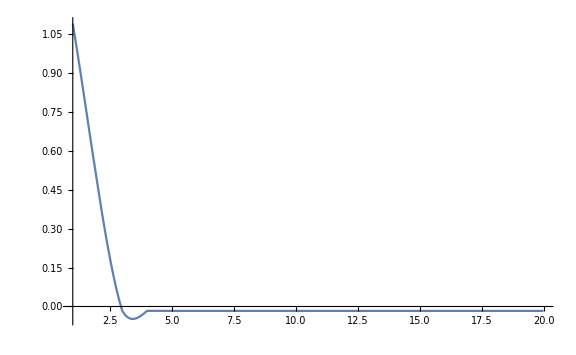

```mathematica
mCent=Floor[M/2];
res[[All,mCent]]//Interpolation//Plot[#[t],{t,1,Kv},PlotRange->Full,ImageSize->Large]&
```

```mathematica
anime=ListAnimate[Table[ListPlot[list,PlotRange->{{1,M},{-0.05,.7}},Joined->True,ImageSize->Large],{list,res}],15]
```

```mathematica
res//TableForm
```

0. | 0.0913683 | 0.181173 | 0.267878 | 0.35 | 0.426133 | 0.494975 | 0.555347 | 0.606218 | 0.646716 | 0.676148 | 0.694011 | 0.7 | 0.694011 | 0.676148 | 0.646716 | 0.606218 | 0.555347 | 0.494975 | 0.426133 | 0.35 | 0.267878 | 0.181173 | 0.0913683 | 0.
0 | 0.0811168 | 0.160846 | 0.237823 | 0.31073 | 0.378321 | 0.439439 | 0.493038 | 0.5382 | 0.574154 | 0.600284 | 0.616144 | 0.62146 | 0.616144 | 0.600284 | 0.574154 | 0.5382 | 0.493038 | 0.439439 | 0.378321 | 0.31073 | 0.237823 | 0.160846 | 0.0811168 | 0
0 | -0.00436866 | -0.00866257 | -0.0128083 | -0.0167348 | -0.020375 | -0.0236666 | -0.0265532 | -0.0289855 | -0.0309219 | -0.0323292 | -0.0331833 | -0.0334696 | -0.0331833 | -0.0323292 | -0.0309219 | -0.0289855 | -0.0265532 | -0.0236666 | -0.020375 | -0.0167348 | -0.0128083 | -0.00866257 | -0.00436866 | 0
0 | 0.00645346 | 0.0127965 | 0.0189206 | 0.0247209 | 0.0300983 | 0.0349607 | 0.0392249 | 0.0428179 | 0.0456783 | 0.0477572 | 0.0490189 | 0.0494419 | 0.0490189 | 0.0477572 | 0.0456783 | 0.0428179 | 0.0392249 | 0.0349607 | 0.0300983 | 0.0247209 | 0.0189206 | 0.0127965 | 0.00645346 | 0
0 | 0.000227864 | 0.00045183 | 0.000668065 | 0.000872869 | 0.00106274 | 0.00123442 | 0.00138499 | 0.00151185 | 0.00161285 | 0.00168625 | 0.0017308 | 0.00174574 | 0.0017308 | 0.00168625 | 0.00161285 | 0.00151185 | 0.00138499 | 0.00123442 | 0.00106274 | 0.000872869 | 0.000668065 | 0.00045183 | 0.000227864 | 0
0 | 0.00128393 | 0.0025459 | 0.0037643 | 0.0049183 | 0.00598814 | 0.00695552 | 0.00780389 | 0.00851874 | 0.00908783 | 0.00950142 | 0.00975244 | 0.00983659 | 0.00975244 | 0.00950142 | 0.00908783 | 0.00851874 | 0.00780389 | 0.00695552 | 0.00598814 | 0.0049183 | 0.0037643 | 0.0025459 | 0.00128393 | 0
0 | -0.000144255 | -0.000286042 | -0.000422934 | -0.00055259 | -0.000672791 | -0.00078148 | -0.000876798 | -0.000957114 | -0.00102105 | -0.00106752 | -0.00109572 | -0.00110518 | -0.00109572 | -0.00106752 | -0.00102105 | -0.000957114 | -0.000876798 | -0.00078148 | -0.000672791 | -0.00055259 | -0.000422934 | -0.000286042 | -0.000144255 | 0
0 | -0.000817252 | -0.00162052 | -0.00239606 | -0.0031306 | -0.00381158 | -0.00442734 | -0.00496735 | -0.00542237 | -0.0057846 | -0.00604786 | -0.00620764 | -0.00626121 | -0.00620764 | -0.00604786 | -0.0057846 | -0.00542237 | -0.00496735 | -0.00442734 | -0.00381158 | -0.0031306 | -0.00239606 | -0.00162052 | -0.000817252 | 0
0 | -0.00120099 | -0.00238143 | -0.00352112 | -0.00460056 | -0.00560129 | -0.00650618 | -0.00729975 | -0.00796841 | -0.00850073 | -0.00888761 | -0.00912241 | -0.00920113 | -0.00912241 | -0.00888761 | -0.00850073 | -0.00796841 | -0.00729975 | -0.00650618 | -0.00560129 | -0.00460056 | -0.00352112 | -0.00238143 | -0.00120099 | 0
0 | -0.000816495 | -0.00161902 | -0.00239384 | -0.0031277 | -0.00380805 | -0.00442324 | -0.00496275 | -0.00541734 | -0.00577924 | -0.00604226 | -0.00620189 | -0.00625541 | -0.00620189 | -0.00604226 | -0.00577924 | -0.00541734 | -0.00496275 | -0.00442324 | -0.00380805 | -0.0031277 | -0.00239384 | -0.00161902 | -0.000816495 | 0
0 | 0.0000266317 | 0.0000528078 | 0.0000780803 | 0.000102017 | 0.000124208 | 0.000144273 | 0.000161871 | 0.000176698 | 0.000188502 | 0.000197081 | 0.000202288 | 0.000204034 | 0.000202288 | 0.000197081 | 0.000188502 | 0.000176698 | 0.000161871 | 0.000144273 | 0.000124208 | 0.000102017 | 0.0000780803 | 0.0000528078 | 0.0000266317 | 0
0 | 0.00086057 | 0.00170642 | 0.00252306 | 0.00329654 | 0.00401362 | 0.00466202 | 0.00523065 | 0.00570978 | 0.00609122 | 0.00636843 | 0.00653668 | 0.00659309 | 0.00653668 | 0.00636843 | 0.00609122 | 0.00570978 | 0.00523065 | 0.00466202 | 0.00401362 | 0.00329654 | 0.00252306 | 0.00170642 | 0.00086057 | 0
0 | 0.0011884 | 0.00235646 | 0.0034842 | 0.00455233 | 0.00554256 | 0.00643796 | 0.00722321 | 0.00788486 | 0.0084116 | 0.00879442 | 0.00902676 | 0.00910466 | 0.00902676 | 0.00879442 | 0.0084116 | 0.00788486 | 0.00722321 | 0.00643796 | 0.00554256 | 0.00455233 | 0.0034842 | 0.00235646 | 0.0011884 | 0
0 | 0.000820718 | 0.00162739 | 0.00240622 | 0.00314388 | 0.00382775 | 0.00444612 | 0.00498842 | 0.00544536 | 0.00580913 | 0.00607351 | 0.00623397 | 0.00628776 | 0.00623397 | 0.00607351 | 0.00580913 | 0.00544536 | 0.00498842 | 0.00444612 | 0.00382775 | 0.00314388 | 0.00240622 | 0.00162739 | 0.000820718 | 0
0 | -0.0000279287 | -0.0000553795 | -0.0000818827 | -0.000106985 | -0.000130257 | -0.0001513 | -0.000169754 | -0.000185303 | -0.000197682 | -0.000206679 | -0.000212139 | -0.00021397 | -0.000212139 | -0.000206679 | -0.000197682 | -0.000185303 | -0.000169754 | -0.0001513 | -0.000130257 | -0.000106985 | -0.0000818827 | -0.0000553795 | -0.0000279287 | 0
0 | -0.00086015 | -0.00170558 | -0.00252183 | -0.00329493 | -0.00401166 | -0.00465974 | -0.00522809 | -0.00570699 | -0.00608824 | -0.00636532 | -0.00653349 | -0.00658987 | -0.00653349 | -0.00636532 | -0.00608824 | -0.00570699 | -0.00522809 | -0.00465974 | -0.00401166 | -0.00329493 | -0.00252183 | -0.00170558 | -0.00086015 | 0
0 | -0.00118853 | -0.00235672 | -0.00348459 | -0.00455283 | -0.00554318 | -0.00643868 | -0.00722401 | -0.00788574 | -0.00841254 | -0.0087954 | -0.00902776 | -0.00910566 | -0.00902776 | -0.0087954 | -0.00841254 | -0.00788574 | -0.00722401 | -0.00643868 | -0.00554318 | -0.00455283 | -0.00348459 | -0.00235672 | -0.00118853 | 0
0 | -0.000820675 | -0.00162731 | -0.0024061 | -0.00314372 | -0.00382755 | -0.00444589 | -0.00498816 | -0.00544508 | -0.00580884 | -0.0060732 | -0.00623365 | -0.00628744 | -0.00623365 | -0.0060732 | -0.00580884 | -0.00544508 | -0.00498816 | -0.00444589 | -0.00382755 | -0.00314372 | -0.0024061 | -0.00162731 | -0.000820675 | 0
0 | 0.0000279153 | 0.0000553531 | 0.0000818437 | 0.000106934 | 0.000130194 | 0.000151227 | 0.000169673 | 0.000185215 | 0.000197588 | 0.00020658 | 0.000212038 | 0.000213868 | 0.000212038 | 0.00020658 | 0.000197588 | 0.000185215 | 0.000169673 | 0.000151227 | 0.000130194 | 0.000106934 | 0.0000818437 | 0.0000553531 | 0.0000279153 | 0
0 | 0.000860154 | 0.00170559 | 0.00252185 | 0.00329495 | 0.00401168 | 0.00465976 | 0.00522812 | 0.00570702 | 0.00608827 | 0.00636535 | 0.00653352 | 0.0065899 | 0.00653352 | 0.00636535 | 0.00608827 | 0.00570702 | 0.00522812 | 0.00465976 | 0.00401168 | 0.00329495 | 0.00252185 | 0.00170559 | 0.000860154 | 0